```mathematica
mhe4=3727.38;
mhe4=3727.409;
BeHe4=20.4812;
(*BeHe4=17.5;*)
mhe4s=mhe4+BeHe4;
mhe17=mhe4+17.5;
mx=0.;
m=mhe4s;
m=3747.8668951982722;
m3=mhe4;
me=0.51099907;
m1=me;
q2min=(2me)^2;
q2max=(m-m3)^2;
qmin=2 me;
qmax=m-m3;
(*
m20.5 --> He4 + q
*)
e3[q_]:=(m^2+m3^2-q^2)/(2m);
p3[q_]:=Sqrt[(m^2-(m3+q)^2)(m^2-(m3-q)^2)]/(2*m);
eq[q_]:=(m^2-m3^2+q^2)/(2m);
pq[q_]:=p3[q];
(*
m17 --> He4 + q
*)
ehe417[mm17_,q_]:=(mm17^2+mhe4^2-q^2)/(2mm17);
phe417[mm17_,q_]:=Sqrt[(mm17^2-(mhe4+q)^2)(mm17^2-(mhe4-q)^2)]/(2*mm17);
eq17[mm17_,q_]:=(mm17^2-mhe4^2+q^2)/(2mm17);
pq17[mm17_,q_]:=phe417[mm17,q];




mp=938.27231;
mn=939.56563;
ep=0.9+mp;
pp=Sqrt[ep^2-mp^2];
mh3=2808.9433;
mh3=2808.92;
s=mp^2+mh3^2+2*mh3*ep; 
ms=Sqrt[s];
ps=pp;
es=Sqrt[pp^2+ms^2]; 
vs=ps/es;
γs=es/ms;
eqls[q_,cos_]:=γs(   eq[q]+vs pq[q]*cos);
pqls[q_,cos_]:=γs(   pq[q]*cos+vs eq[q]);
e3ls[q_,cos_]:=γs(   e3[q]-vs p3[q]*cos);
p3ls[q_,cos_]:=γs (-p3[q]*cos+vs e3[q]);
(*20.5-->17.5+gamma *)
e17cm[mmx_]:=(m^2+mhe17^2-mmx^2)/(2m);
p17cm[mmx_]:=Sqrt[(m^2-(mhe17+mmx)^2)(m^2-(mhe17-mmx)^2)]/(2*m);

excm[mmx_]:=(m^2-mhe17^2+mmx^2)/(2m);
pxcm[mmx_]:=Sqrt[excm[mmx]^2-mmx^2];

(* Boost 17.5 to the lab system *)
e17ls[mmx_,cos_]:=γs(   e17cm[mmx]+vs p17cm[mmx]*cos);
p17ls[mmx_,cos_]:=γs(   p17cm[mmx]*cos+vs e17cm[mmx]);

(* Boost gamma to the lab system *)
exls[mmx_,cos_]:=γs(   excm[mmx]-vs pxcm[mmx]*cos);
pxls[mmx_,cos_]:=γs(   -pxcm[mmx]*cos+vs excm[mmx]);

(* v and gamma of 17.5 in the lab system *)
v[mmx_,cos_]:=p17ls[mmx,cos]/e17ls[mmx,cos];
γ[mmx_,cos_]:=e17ls[mmx,cos]/mhe17;

(* Boost e+e- to the lab system *)
(* need q in the decay 17.5--> He+q *)
eq17ls[q_,mmx_,cos1_,mm17_,cos2_]:=γ[mmx,cos1](   eq17[mm17,q]+v[mmx,cos1] pq17[mm17,q]*cos2);
pq17ls[q_,mmx_,cos1_,mm17_,cos2_]:=γ[mmx,cos1](   pq17[mm17,q]*cos2+v[mmx,cos1] eq17[mm17,q]);

ehels[q_,mmx_,cos1_,mm17_,cos2_]:=γ[mmx,cos1](   ehe417[mm17,q]-v[mmx,cos1] phe417[mm17,q]*cos2);
phels[q_,mmx_,cos1_,mm17_,cos2_]:=γ[mmx,cos1](   -phe417[mm17,q]*cos2+v[mmx,cos1] ehe417[mm17,q]);
```

```mathematica
mx=2.;
cs=1.;
cs2=1.
mq=17.;
m17=mhe4+18.5;

Print["M He* = ",m]
Print[" M20,5-->he4+q"]
Print["E He4 = ",e3[mq]]
Print["P He4 = ",p3[mq]]
Print["E q = ",eq[mq]]
Print["P q = ",pq[mq]]
Print["--------------"]
Print["M He* = ",m17]
Print[" M17-->he4+q"]
Print["E He4 = ",ehe417[m17,mq]]
Print["P He4 = ",phe417[m17,mq]]
Print["E q = ",eq17[m17,mq]]
Print["P q = ",pq17[m17,mq]]

Print["--------------"]
Print["Laboratory system "]
Print[" M17-->he4+q"]
Print["E He4 = ",e17ls[mx,cs]]
Print["P He4 = ",e17ls[mx,cs]]
Print["v = ",v[mx,cs]]
Print["γ = ",γ[mx,cs]]
Print["eq17ls[q,mmx,cos1,m17,cs2] = ",eq17ls[mq,mx,cs,m17,cs2]]
Print["pq17ls[q,mmx,cos1,m17,cs2] = ",pq17ls[mq,mx,cs,m17,cs2]]
```

1.

M He* = 3747.87

M20,5-->he4+q

E He4 = 3727.43

P He4 = 11.3498

E q = 20.4406

P q = 11.3498

--------------

M He* = 3745.91

M17-->he4+q

E He4 = 3727.42

P He4 = 7.27922

E q = 18.4929

P q = 7.27922

--------------

Laboratory system

M17-->he4+q

E He4 = 3745.16

P He4 = 3745.16

v = 0.0115488

γ = 1.00007

eq17ls[q,mmx,cos1,m17,cs2] = 18.5782

pq17ls[q,mmx,cos1,m17,cs2] = 7.49329

```mathematica
m17=17.0;
cs=1.;
ms
m
eqls[m17,cs]
e3ls[m17,cs]
Print ["vs ",vs ]
Print [" ms γs = ",ms γs]
Print["E sum ls = ",e3ls[m17,cs]+eqls[m17,cs]]
eq0=17.5;
pq0=Sqrt[eq0^2-m17^2];
mx=0;
eq1=γ[mx](eq0+v[mx]pq0);
pq1=γ[mx](pq0+v[mx]eq0);
eq2=γs(eq0+vs pq0);
pq2=γs(pq0+vs eq0);
eq2
pq2
Sqrt[eq2^2-pq2^2]
eqls[17.,0.]
pqls[17.,0.]
eq[17.]
```

3747.87

3747.87

20.5663

3727.53

vs 0.0109672

ms γs = 3748.09

E sum ls = 3748.09

17.5466

4.3455

17.

20.4418

0.224189

20.4406

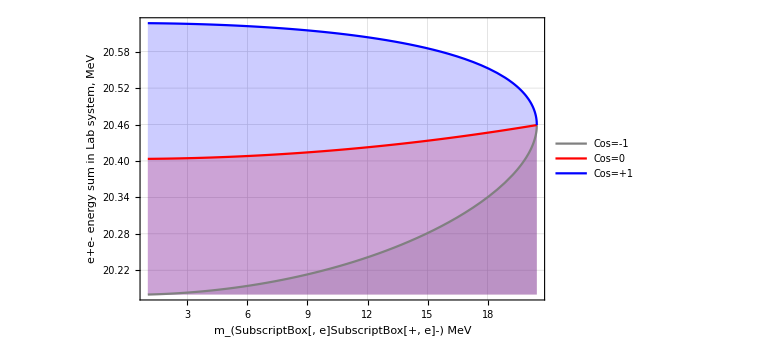

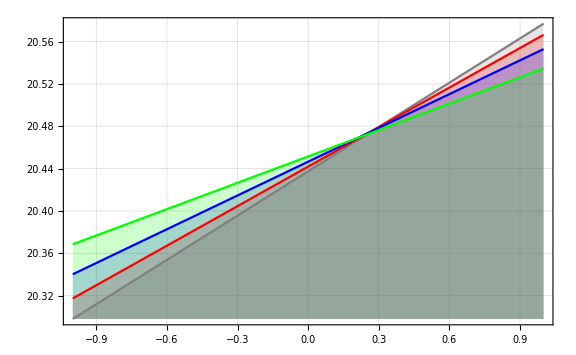

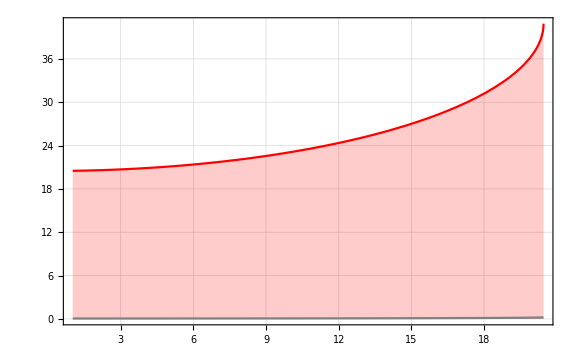

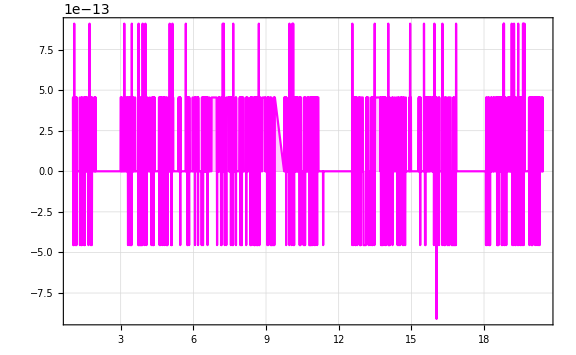

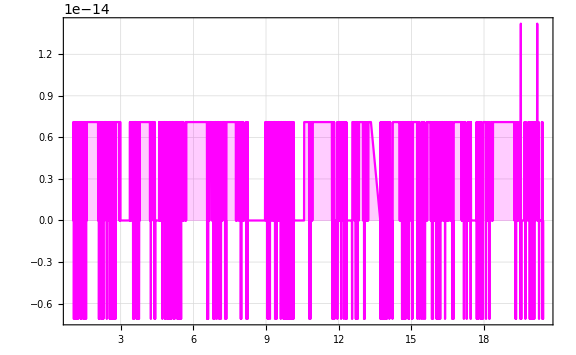

```mathematica
Plot[{eqls[x,-1.],eqls[x,0.],eqls[x,+1.]},{x,qmin,qmax},
PlotRange->All,
Frame->True,
Frame ->True, FrameLabel->{"m_(SubscriptBox[, e]SubscriptBox[+, e]-)   MeV","e+e- energy sum in Lab system, MeV"},
Filling->Axis,
PlotStyle->{Gray,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
PlotLegends->Placed[{"Cos=-1","Cos=0","Cos=+1"},Center],
GridLines->Automatic]

Plot[{eqls[16.,cos],eqls[17.,cos],eqls[18.,cos],eqls[19.,cos]},{cos,-1.,1.},
PlotRange->All,
Frame->True,
Filling->Axis,
PlotStyle->{Gray,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic
]
Plot[{e3ls[x,1.]-mhe4,p3ls[x,1.]},{x,qmin,qmax},
PlotRange->All,
Frame->True,
Filling->Axis,
PlotStyle->{Gray,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic
]
Plot[{e3ls[x,1.]+eqls[x,1.]-ep-mh3},{x,qmin,qmax},
PlotRange->All,
Frame->True,
Filling->Axis,
PlotStyle->{Gray,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic
]
Plot[{p3ls[x,1.]+pqls[x,1.]-pp},{x,qmin,qmax},
PlotRange->All,
Frame->True,
Filling->Axis,
PlotStyle->{Gray,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic
]
```

```mathematica
mhe4s
```

3744.88

```mathematica
0.9/mhe4s*0.9
```

0.000216295

```mathematica
(ms^2+(ms-3.)^2)/2/ms-(ms-3.)
```

0.0012009

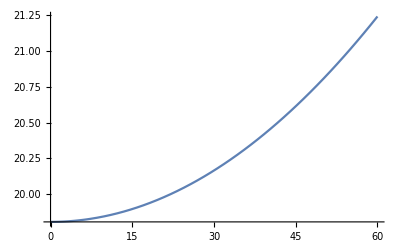

```mathematica
ss[pv_]:=mp^2+mh3^2+2*mh3*Sqrt[pv^2+mp^2]; 
mss[pv_]:=Sqrt[ss[pv]];
Plot[mss[x]-mhe4,{x,0,60}]
```

```mathematica
ecm[17.]+e3cm[17.]
ecm[1.]+e3cm[1.]
```

3748.12

3748.12